```mathematica
dataD={0.991,0.990,0.989,0.990,0.990};
```

```mathematica
dataD=Quantity[dataD//Mean,"mm"]
```

0.99 mm

```mathematica
dataT={{18.17,17.9,18.01,18.1,17.92},{15.63,15.7,16.,15.85,15.56},{14.06,14.11,14.1,13.9,13.91},{12.2,12.07,11.98,11.86,11.71},{10.73,10.25,10.76,10.66,10.56},{9.05,9.,9.13,9.03,9.03}};
```

```mathematica
Table[MeanAround[dataT[[i]]],{i,1,6}]
```

{18.020.05,15.750.08,14.020.05,11.960.08,10.590.09,9.0480.022}

```mathematica
v0=Quantity[10*10^(-2)/Table[MeanAround[dataT[[i]]],{i,1,6}],"m/s"]
```

{(0.0055490.000016) m/s,(0.0063500.000032) m/s,(0.0071350.000023) m/s,(0.008360.00006) m/s,(0.009440.00008) m/s,(0.0110520.000027) m/s}

```mathematica
ρ=Quantity[7.8*10^3,"kg/m^3"]
```

7800. kg/m^3

```mathematica
ρ0=Quantity[0.95*10^3,"kg/m^3"]
```

950. kg/m^3

```mathematica
d=Quantity[2*10^-2,"m"]
```

1/50 m

```mathematica
g=Quantity[9.794,"m/s^2"]
```

9.794 m/s^2

```mathematica
η=UnitConvert[((ρ-ρ0)g dataD^2)/(18v0(1+2.4 dataD/d)),"Pa s"]
```

{(0.58840.0017) s Pa,(0.51420.0026) s Pa,(0.45760.0015) s Pa,(0.39060.0028) s Pa,(0.34580.0030) s Pa,(0.29540.0007) s Pa}

```mathematica
t=Table[x,{x,26.1,36.1,2}]
```

{26.1,28.1,30.1,32.1,34.1,36.1}

```mathematica
xx=Table[{t[[i]],QuantityMagnitude[η[[i]]]},{i,1,6}]
```

{{26.1,0.58840.0017},{28.1,0.51420.0026},{30.1,0.45760.0015},{32.1,0.39060.0028},{34.1,0.34580.0030},{36.1,0.29540.0007}}

```mathematica
LinearModelFit[xx,x,x]
```

FittedModel[…]

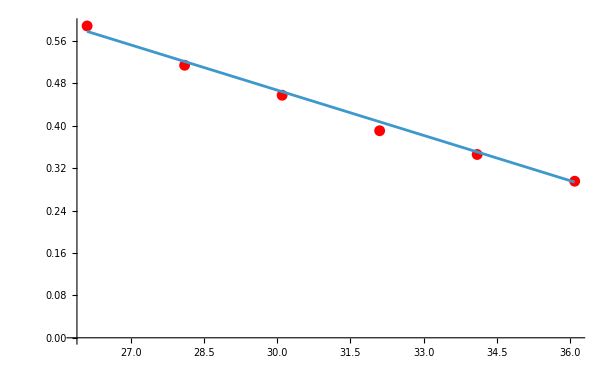

```mathematica
Show[ListPlot[xx,PlotStyle->Red],Plot[%59[x],{x,26.1,36.1}]]
```

```mathematica
xx
```

{{26.1,0.58840.0017},{28.1,0.51420.0026},{30.1,0.45760.0015},{32.1,0.39060.0028},{34.1,0.34580.0030},{36.1,0.29540.0007}}

```mathematica
Grid[%62]
```

26.1 | 0.58840.0017
28.1 | 0.51420.0026
30.1 | 0.45760.0015
32.1 | 0.39060.0028
34.1 | 0.34580.0030
36.1 | 0.29540.0007